```mathematica
Binary Celular Automata for Language Recognition
						
																													    Ferran Ramírez Martí
```

```mathematica
AFD={{q,p,r},{a,b,c,d},{{1,a,1},{1,b,2},{2,a,3},{2,b,2},{3,a,3},{3,b,3}},q,{r}}
   ACu={{a,b,c,d},{{a,b,q},{a,b,q},{a,b,q}},{a,b,c,d,q,p,r}};
ACb={{a,b,c,d},{{a,b,q},{a,b,q},{a,b,q}},{a,b,c,d,q,p,r}}
```

```mathematica
(* Genera un Autómata Celular Unidireccional Unidimensional que acepte un mismo lenguaje que pueda
aceptar un Autómata Finito Determinista dado como entrada *)
ACaceptorU[AFD_]:=Module[{ACu},
ACu={};
AppendTo[ACu,Union[AFD[[1]],AFD[[2]] ] ]; (*Junta estados y símbolos*)
AppendTo[ACu, AFD[[3]] ];  (*Copia las transiciones*)
AppendTo[ACu, AFD[[5]] ]; (*Copia el estado final*)
(*Añade a la lista de transiciones, todas los posibles estados generados al concatenar AFD[[2]] consigo mismo*)
For[i=1, i<= Length[AFD[[2]] ], i++ ,
For[j=1, j<= Length[AFD[[2]] ], j++ ,
AppendTo[ACu[[2]],{AFD[[2]][[i]],AFD[[2]][[j]],AFD[[2]][[j]]} ];
] ;
] ;
(*Añade a la lista de transiciones, todas los posibles estados generados al concatenar AFD[[1]] consigo mismo*)
For[i=1, i<= Length[AFD[[1]] ], i++ ,
For[j=1, j<= Length[AFD[[1]] ], j++ ,
AppendTo[ACu[[2]],{AFD[[1]][[i]],AFD[[1]][[j]],AFD[[1]][[j]]} ];
] ;
] ;
Return[ ACu];
]
```

```mathematica
acu=ACaceptorU[  {{q,r,p},{a,b},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r}},q,{r}}]
```

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b},{q,q,q},{q,r,r},{q,p,p},{r,q,q},{r,r,r},{r,p,p},{p,q,q},{p,r,r},{p,p,p}},{r}}

```mathematica
(*###############################################################################################################################*)
```

```mathematica
(* Dado un Autómata Celular reconocedor de un lenguaje y una cadena, indica si pertenece o no al lenguaje (True o False) 
	iniS_ : estado de frontera inicial *)
PerteneceA[ACu_, cadena_, iniS_]:=Module[{pertenece, aux, dist, match},
pertenece=False;
aux={}; (*Lista con las listas con las configuraciones generadas en cada iteración*)
dist= StringLength[cadena];
(*Metemos la iteración 0; el estado inicial en aux en forma de símbolos*)
AppendTo[aux, StringSplit[cadena,""]];
For[i=1, i≤dist, i++,
aux[[1]][[i]]=ToExpression[aux[[1]][[i]]];
];
(*Genera y añade las nuevas configuraciones a aux según los estados que hagan match en el ACu dado*)
For[i=2, i≤dist+2, i++,
AppendTo[aux,{}];
match= Cases[ACu [[2]],{iniS,aux[[i-1]][[1]],_}];
(*Devuelve falso si no hay match, AC no lo reconoce.*)
If[match== {}, Return[False],AppendTo[aux[[i]],match[[1]][[3]]] ];
For[j=2, j≤dist, j++,
match=Cases[ACu [[2]],{aux[[i-1]][[j-1]],aux[[i-1]][[j]],_}];
If[match=={}, Return[False],AppendTo[aux[[i]],match[[1]][[3]] ] ];
]
];
(*Si el valor de la última celda en la última iteración coincide con el estado final de ACu, True; si no, False*)
(*Return[aux];*)
If[aux[[dist+1]][[dist]]==ACu[[3]][[1]], Return[True], Return[False]];
]
```

```mathematica
PerteneceA[{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b},{q,q,q},{q,r,r},{q,p,p},{r,q,q},{r,r,r},{r,p,p},{p,q,q},{p,r,r},{p,p,p}},{r}},"ababaaaa",q]
```

```mathematica
(*##################################################################################################################################*)
```

```mathematica
(* Genera un Autómata Celular Bidireccional Unidimensional a partir de un Autómata Finito Determinista *)
(* Este algoritmo formaría sus estados, uniendo el último elemento de la transición que coincida con el elemento de la célula en cuestión. Para 2 transiciones: (p,a,r) y (q,a,p), el estado de transición de una célula p sería (a,p,a,r) donde r sería el nuevo síḿbolo
y a, y a, las vecinas de p *)
ACaceptorB[AFD_]:=Module[{ACu},
ACu={};
AppendTo[ACu,Union[AFD[[1]],AFD[[2]] ] ];
AppendTo[ACu, AFD[[3]] ];
AppendTo[ACu, AFD[[5]] ];
For[i=1, i<= Length[AFD[[2]] ], i++ ,
For[j=1, j<= Length[AFD[[2]] ], j++ ,
For[k=1, k<= Length[AFD[[2]] ], k++ ,
AppendTo[ACu[[2]],{AFD[[2]][[i]],AFD[[2]][[j]],AFD[[2]][[k]],AFD[[2]][[j]]} ];
]
] 
] ;
For[i=1, i<= Length[AFD[[1]] ], i++ ,
For[j=1, j<= Length[AFD[[1]] ], j++ ,
For[k=1, k<= Length[AFD[[1]] ], k++ ,
AppendTo[ACu[[2]],{AFD[[1]][[i]],AFD[[1]][[j]],AFD[[1]][[k]],AFD[[1]][[j]]} ];
]
] 
] ;
Return[ ACu ];
]
```

```mathematica
acu=ACaceptorB[  {{q,r,p},{a,b},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r}},q,{r}}]
```

```mathematica
{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r},{a,a,a,a},{a,a,b,a},{a,b,a,b},{a,b,b,b},{b,a,a,a},{b,a,b,a},{b,b,a,b},{b,b,b,b},{q,q,q,q},{q,q,r,q},{q,q,p,q},{q,r,q,r},{q,r,r,r},{q,r,p,r},{q,p,q,p},{q,p,r,p},{q,p,p,p},{r,q,q,q},{r,q,r,q},{r,q,p,q},{r,r,q,r},{r,r,r,r},{r,r,p,r},{r,p,q,p},{r,p,r,p},{r,p,p,p},{p,q,q,q},{p,q,r,q},{p,q,p,q},{p,r,q,r},{p,r,r,r},{p,r,p,r},{p,p,q,p},{p,p,r,p},{p,p,p,p}},{r}}
```

```mathematica
(*##################################################################################################################################*)
```

```mathematica
(* Devuelve la secuencia de computación que se lleva a cabo en el módulo 2 mediante un diagrama espaciotemporal
	No se usa el módulo dos por un error a solucionar *)
Secuencia[ACu_, cadena_, iniS_]:=Module[{pertenece, aux, dist, match},
pertenece=False;
aux={}; (*Lista con las listas con las configuraciones generadas en cada iteración*)
dist= StringLength[cadena];
(*Metemos la iteración 0; el estado inicial en aux en forma de símbolos*)
AppendTo[aux, StringSplit[cadena,""]];
For[i=1, i≤dist, i++,
aux[[1]][[i]]=ToExpression[aux[[1]][[i]]];
];
(*Genera y añade las nuevas configuraciones a aux según los estados que hagan match en el ACu dado*)
For[i=2, i≤dist+2, i++,
AppendTo[aux,{}];
match= Cases[ACu [[2]],{iniS,aux[[i-1]][[1]],_}];
(*Si no cumple el match, no pertenece por lo que se escriben celdas con 1, en el ArayPlot en negro, indicando dónde lo ha detectado.*)
If[match== {}, AppendTo[aux[[i]], 1],AppendTo[aux[[i]],match[[1]][[3]]] ];
For[j=2, j≤dist, j++,
match=Cases[ACu [[2]],{aux[[i-1]][[j-1]],aux[[i-1]][[j]],_}];
If[match=={}, AppendTo[aux[[i]], 1],AppendTo[aux[[i]],match[[1]][[3]] ] ];
]
];
Return[ArrayPlot [ aux,ColorRules->{a->Red,b->Blue, q->Yellow,p->Purple,r->Green}]];
]
```

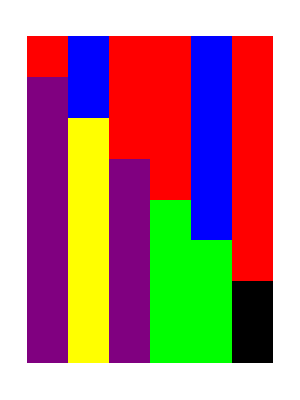

```mathematica
Secuencia[{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,b,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b},{q,q,q},{q,r,r},{q,p,p},{r,q,q},{r,r,r},{r,p,p},{p,q,q},{p,r,r},{p,p,p}},{r}},"abaaba",q]
```